```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
<<GDCComparisons`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Get::noopen: Cannot open DialecticalStructures`GDCAnalysis3`.

Needs::nocont: Context DialecticalStructures`GDCAnalysis3` was not created when Needs was evaluated.

```mathematica
compACCheFunc[nam_, accE_, accH_, colTS_, labP_]:=Module[{data0,data1,data2, colTSRed, labPRed},
	Which[nam=="DLB",
	colTSRed=colTS;
labPRed=labP;,
	nam=="MUR",
	colTSRed=Drop[colTS,2];
labPRed=Drop[labP,2];,
	nam=="LYE",
	colTSRed=Drop[colTS,2];
labPRed=Drop[labP,2];,
	nam=="PHI",
	colTSRed=Drop[colTS,4];
labPRed=Drop[labP,4];,
	nam=="SED",
	colTSRed=Drop[colTS,6];
labPRed=Drop[labP,6];,
	nam=="AUS",
	colTSRed=Drop[colTS,12];
labPRed=Drop[labP,12];];

data0=Map[{accE[[nam]][[#,2]],accH[[nam]][[#,2]]}&,Range[Length[accE[[nam]]]]];
data1=Sort@Map[{accE[[nam]][[#,2]],accH[[nam]][[#,2]],colTSRed[[#]]}&,Range[Length[accE[[nam]]]]];
data2=Map[Labeled[data1[[#]][[1;;2]],data1[[#]][[3]],labPRed[[#]]]&,Range[Length[data1]]];
Return[{data2,data0}];
];
compACChePlot[nam_, data_, col_]:=Module[{plot},
(*{{0.6734693877551021,0.8928571428571429},{0.5333333333333333,1.}}*)
plot=ListPlot[data,PlotRange->{{0.66,0.9},{0.5,1.05}},  PlotMarkers->{{"●",15},{"●",15}}, PlotStyle-> {{col,Thick},{col, Dashed}},PlotLegends->{None,nam},PlotLabel->"Similarity with the Final Consens",Frame->True,FrameLabel->{"ACC(e)","ACC(h)"},RotateLabel->{False,True},Joined->{False,True}, ImageSize->1200];
Return[plot];
];
compACChePlot2[datAll_, namesAll_, colorAll_]:=Module[{plot},
plot=ListPlot[Flatten[datAll,1],PlotRange->All,  PlotMarkers->{{"●",15},{"●",15},{"●",15},{"●",15},{"●",15},{"●",15}}, PlotStyle-> {{colorAll[[1]],Thick},{colorAll[[1]], Dashed},{colorAll[[2]],Thick},{colorAll[[2]], Dashed},{colorAll[[3]],Thick},{colorAll[[3]], Dashed},{colorAll[[4]],Thick},{colorAll[[4]], Dashed},{colorAll[[5]],Thick},{colorAll[[5]], Dashed},{colorAll[[6]],Thick},{colorAll[[6]], Dashed}},PlotLegends->{None,namesAll[[1]],None,namesAll[[2]],None,namesAll[[3]],None,namesAll[[4]],None,namesAll[[5]],None,namesAll[[6]]},PlotLabel->"Similarity with the Final Consens",Frame->True,FrameLabel->{"ACC(e)","ACC(h)"},RotateLabel->{False,True},Joined->{False,True}, ImageSize->1200];
Return[plot];
];
```

```mathematica
accEVBK=Get["/home/carla/GDC/Comparisons/Veritism/ACC/gdc_ACC_EVBK.txt"];
accCH=Get["/home/carla/GDC/Comparisons/Veritism/CH/gdc_ACC_CH.txt"];
names=Map[StringTake[#,{-7,-5}]&,doj]
```

{AUS,DLB,LYE,MUR,PHI,SED}

```mathematica
accEVBK[["DLB"]][[1;;3]]
accCH[["DLB"]][[1;;3]]
```

{{0,0.6,1.},{0.5,0.6,1.},{1,0.6,1.}}

{{0,0.72973},{0.5,0.75},{1,0.763636}}

{{0,0.6},{0.5,0.6},{1,0.6}}

```mathematica
timesteps={"0","1a","1b","2a","2b","3a","3b","4a","4b","5a","5b","6a","6b","7a","7b","8a", "8b"};
colorList=Map[ColorData["BlueGreenYellow"][#]&,Range[Length[timesteps]]/Length[timesteps]];
coloredTimeSteps=Map[Style[timesteps[[#]],colorList[[#]], Bold,14]&,Range[Length[timesteps]]]
(*labelPosition={Left, Top, Right, Bottom, Left, Top, Right, Bottom,Left, Top, Right, Bottom,Left, Top, Right, Bottom,Left };*)
labelPosition={Top, Bottom, Top, Bottom,Top, Bottom, Top, Bottom,Top, Bottom, Top, Bottom,Top, Bottom, Top, Bottom,Top };
```

{0,1a,1b,2a,2b,3a,3b,4a,4b,5a,5b,6a,6b,7a,7b,8a,8b}

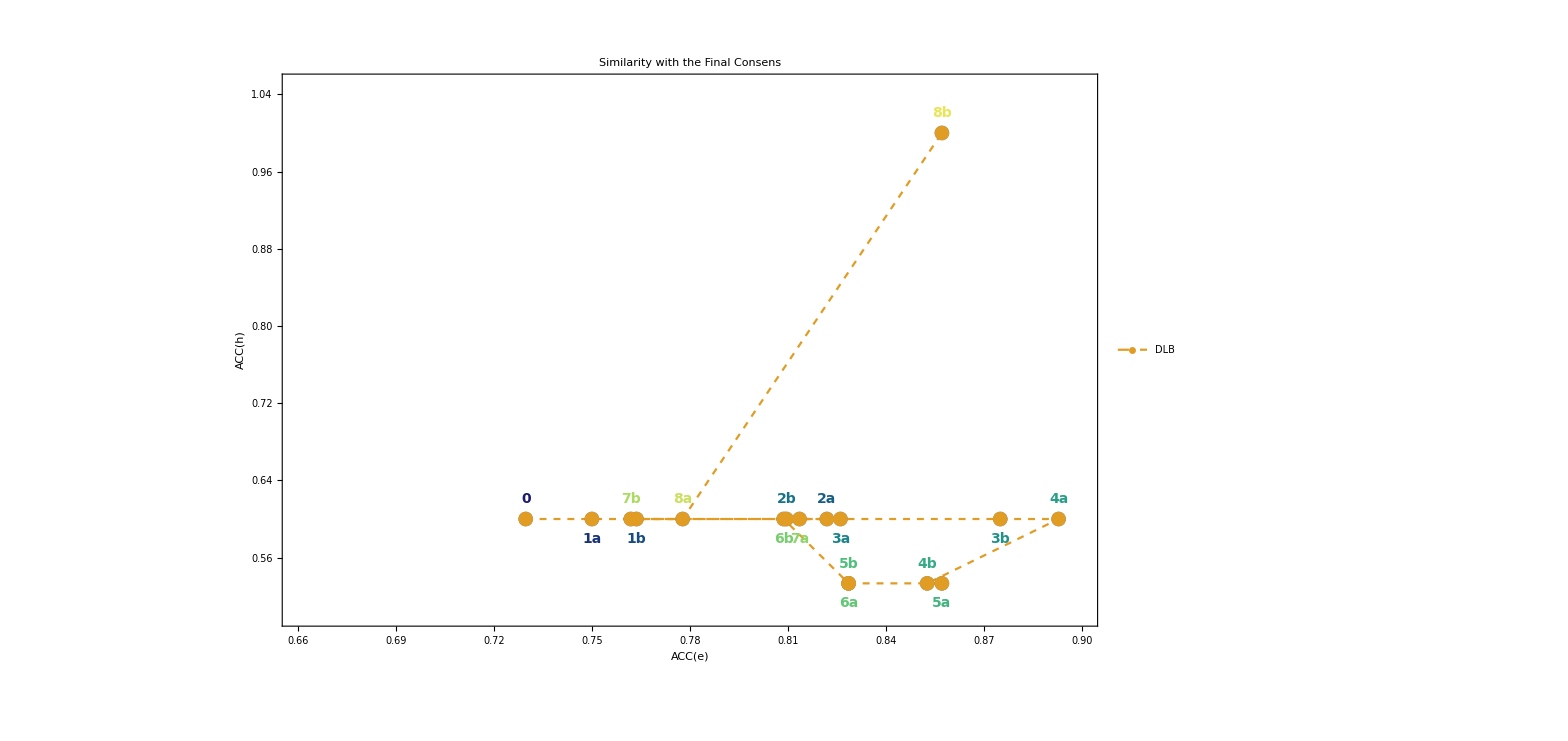

```mathematica
dlbData=compACCheFunc["DLB", accEVBK, accCH, coloredTimeSteps, labelPosition];
dlbPlot=compACChePlot["DLB", dlbData, "Orange"]
```

```mathematica
colorList2={Blue, Red, Purple, Green, Yellow, Orange};
```

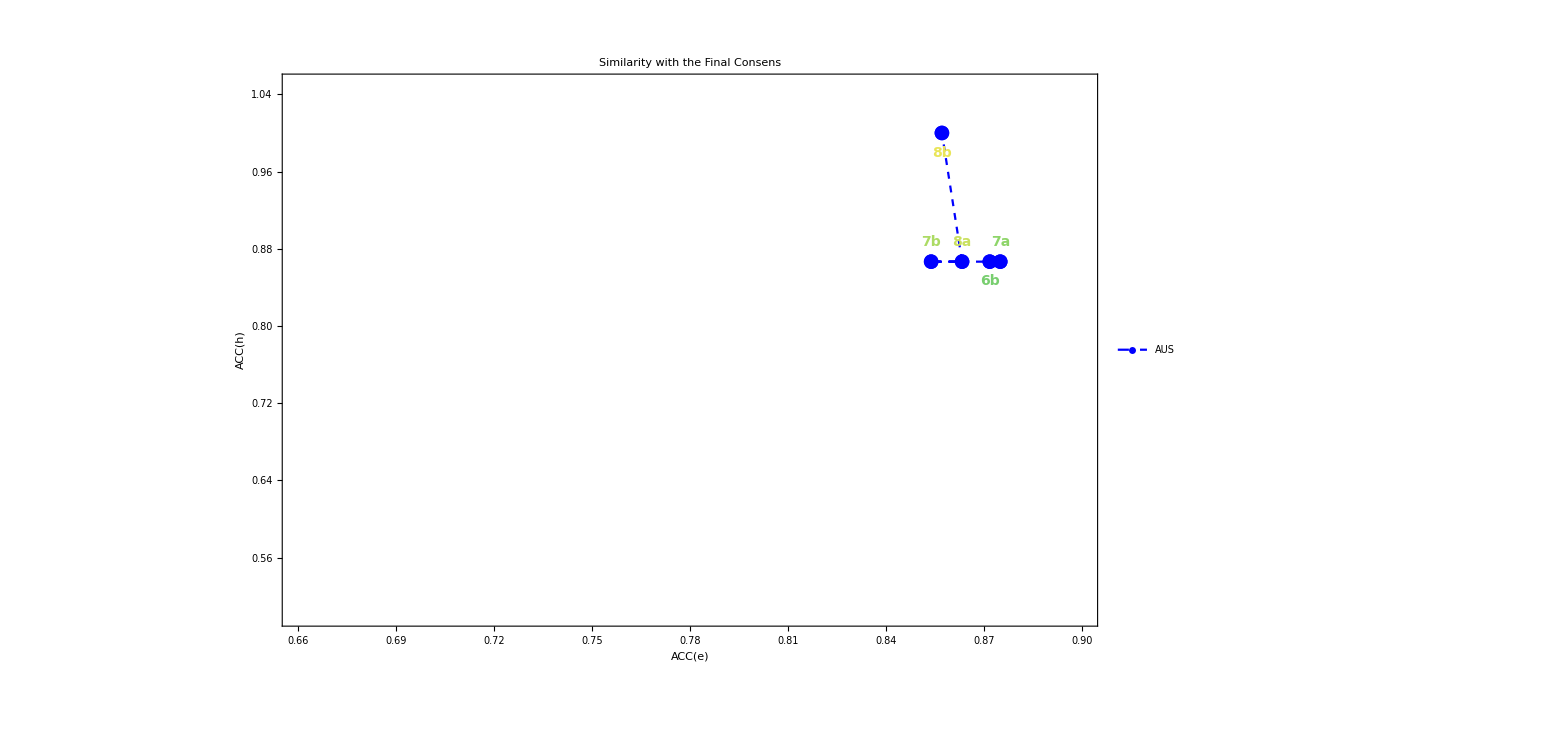
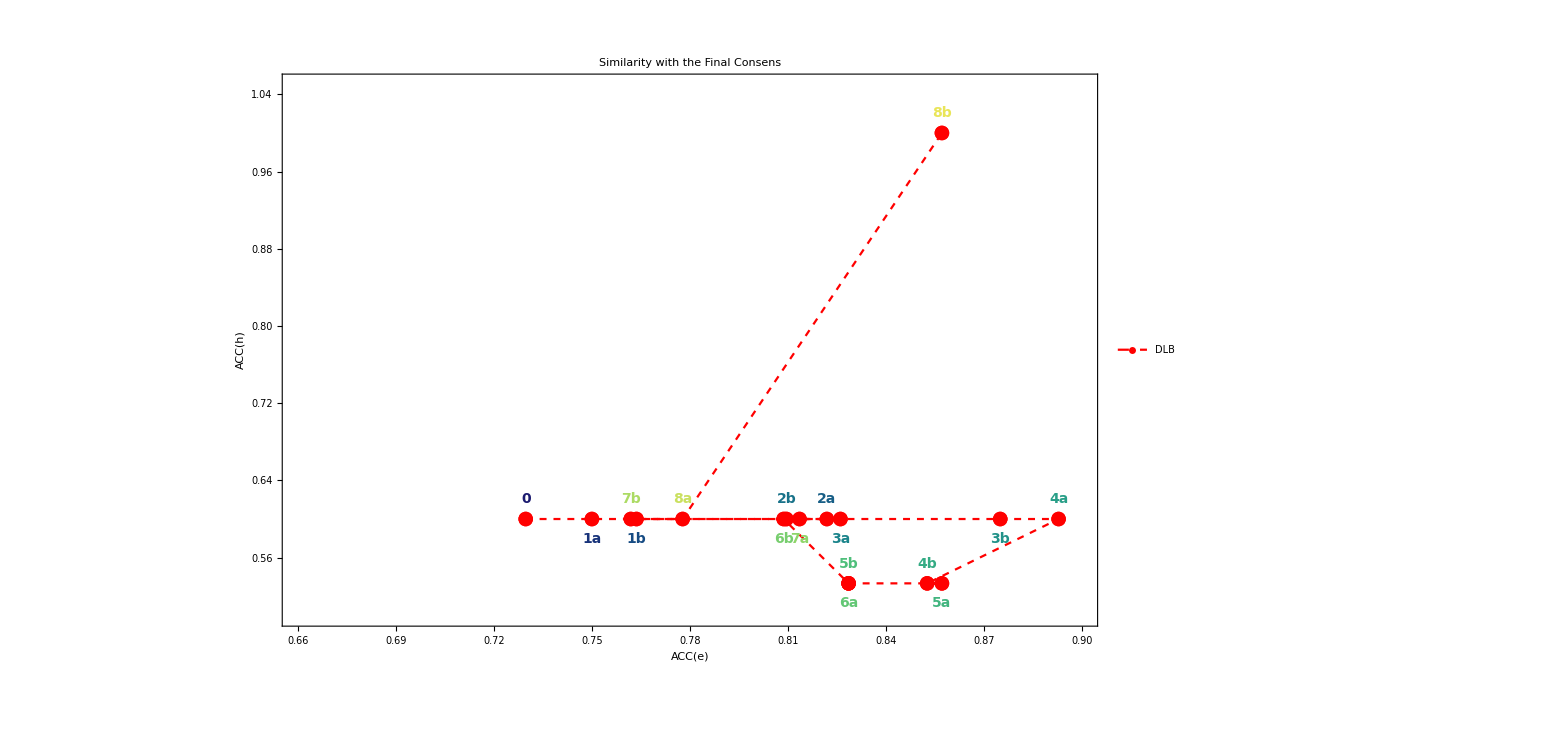
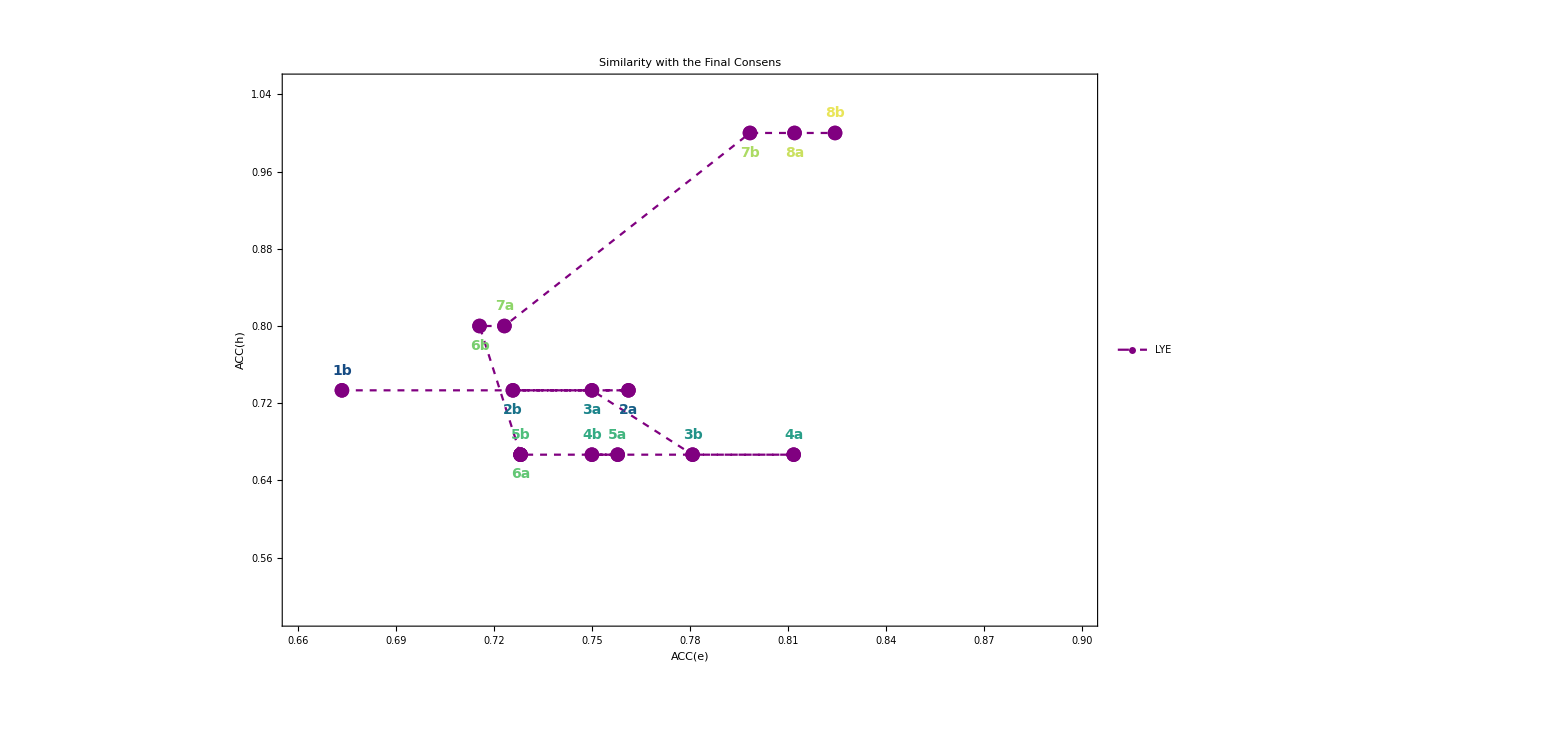
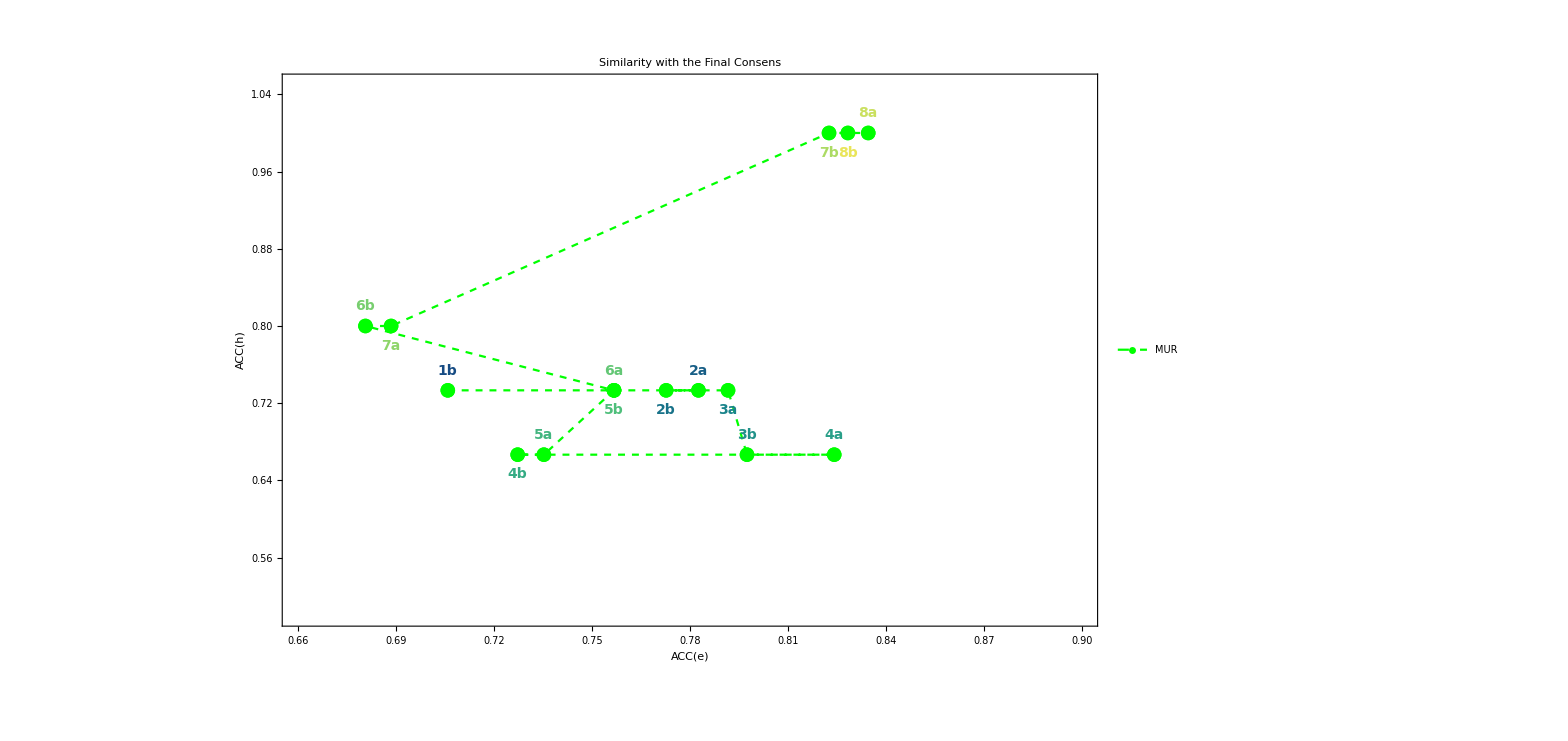
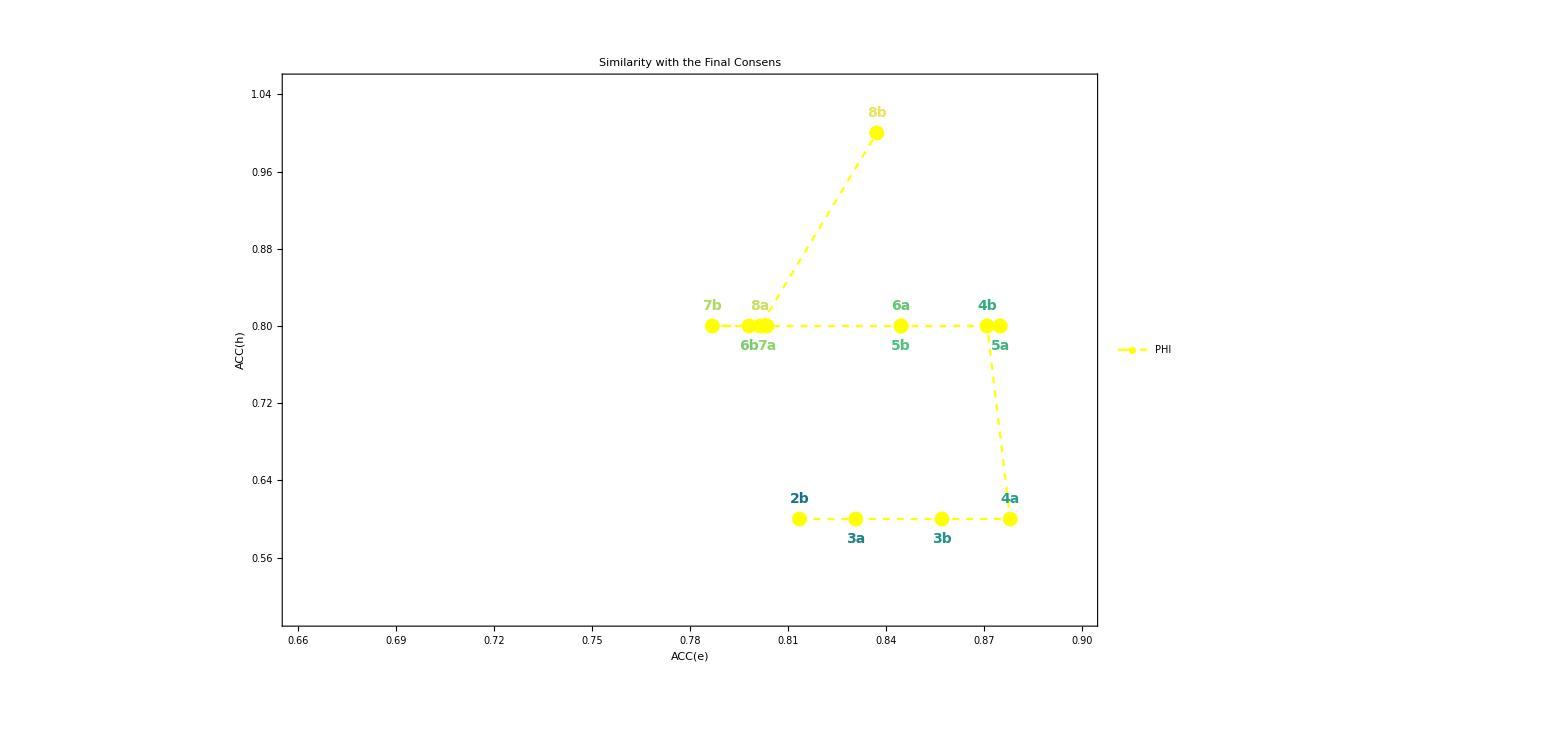
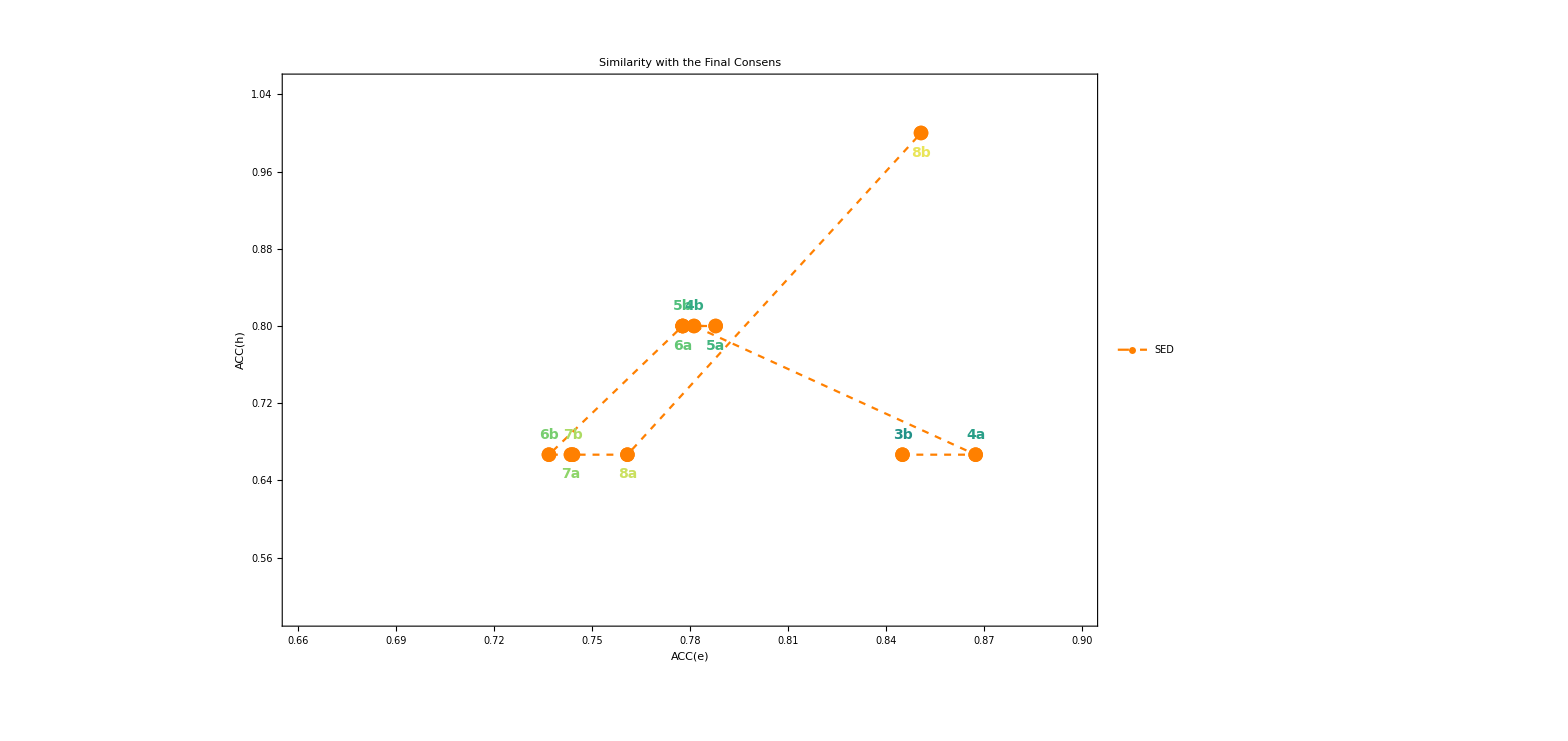
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
dataAll=Map[compACCheFunc[#, accEVBK, accCH, coloredTimeSteps, labelPosition]&,names];plotAll=Map[compACChePlot[names[[#]], dataAll[[#]], colorList2[[#]]]&,Range[Length[names]]];
plotsOut=Grid[{plotAll[[1;;2]],plotAll[[3;;4]],plotAll[[5;;6]]}, ItemSize->95]
```

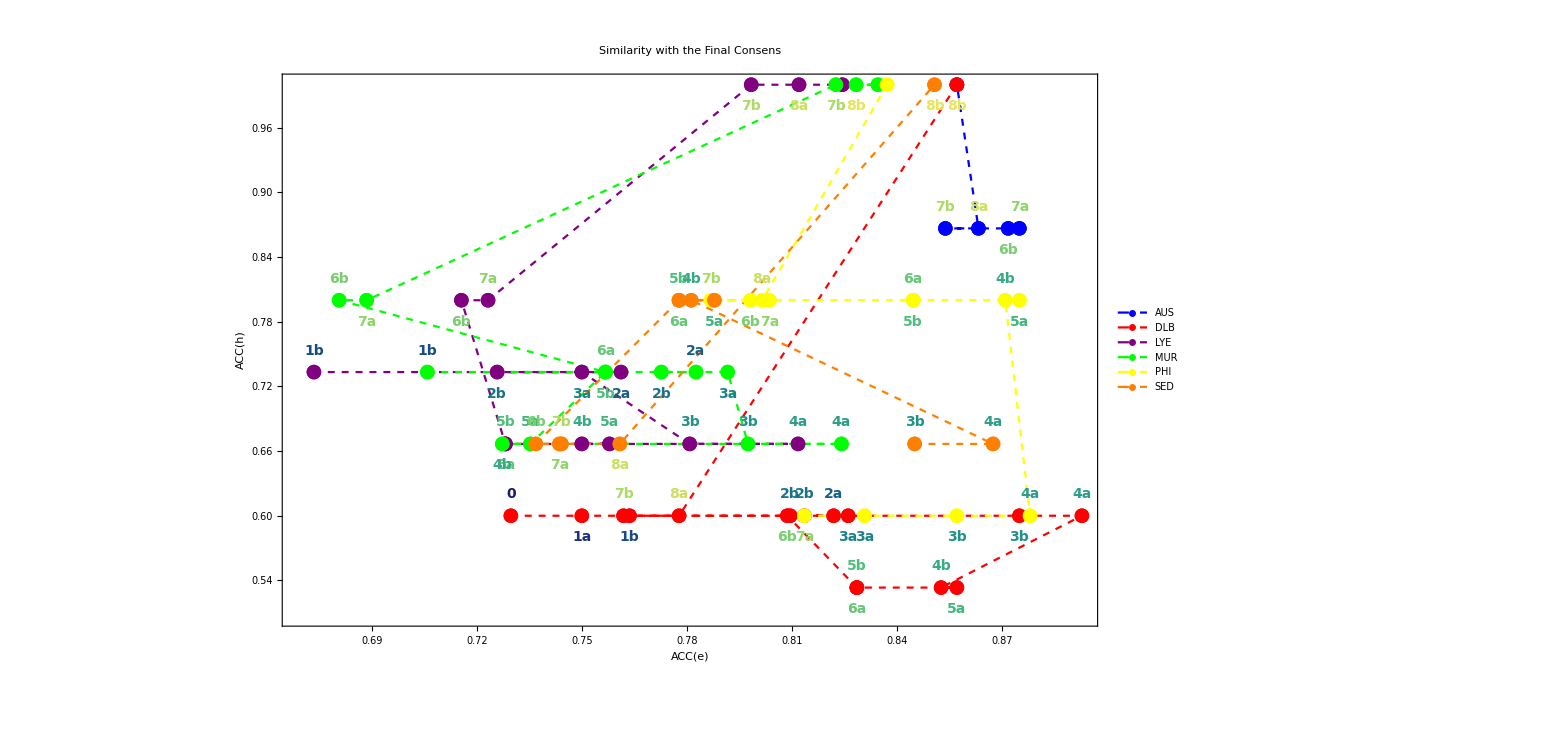

```mathematica
plotAllIn=compACChePlot2[dataAll, names, colorList2]
```

```mathematica
SetDirectory["/home/carla/GDC/Comparisons/New/Veritism/"]
Export["All_In_One_ACC_h_ACC_e.jpeg",plotAllIn,ImageResolution->200]
Map[Export[ToString[names[[#]]]<>"_ACC_h_ACC_e.jpeg",plotAll[[#]],ImageResolution->200]&, Range[Length[names]]]
```

/home/carla/GDC/Comparisons/New/Veritism

ACC_h_ACC_e.jpeg

All_In_One_ACC_h_ACC_e.jpeg

{AUS_ACC_h_ACC_e.jpeg,DLB_ACC_h_ACC_e.jpeg,LYE_ACC_h_ACC_e.jpeg,MUR_ACC_h_ACC_e.jpeg,PHI_ACC_h_ACC_e.jpeg,SED_ACC_h_ACC_e.jpeg}

```mathematica
Export["Grid_ACC_h_ACC_e.jpeg",plotsOut,ImageResolution->200]
```

Grid_ACC_h_ACC_e.jpeg

```mathematica
dataLim=Flatten[dataAll[[All,2]],1];
{{Min@dataLim[[All,1]],
Max@dataLim[[All,1]]},
{Min@dataLim[[All,2]],
Max@dataLim[[All,2]]}}
```

{{0.673469,0.892857},{0.533333,1.}}